```mathematica
(*Params*)
NN=500; (* Number of finite elements *)
α=2/180*Pi; (* AOA *)
uinf={Cos[α],Sin[α]}; (* Velicity vector Subscript[v, ∞] *)
```

```mathematica
Source[x_,y_,x1_,x2_]:=Block[{r1,r2,θ1,θ2,ϕ,u,v},
r1=(x-x1)^2+y^2;
 r2=(x-x2)^2+y^2;
θ1=ArcTan[x1-x,-y]+Pi; 
θ2=ArcTan[x2-x,-y]+Pi; 
ϕ=1/(4 Pi)*((x-x1)Log[r1]-(x-x2)Log[r2]+2 y (θ2-θ1)); 
u=1/(4 Pi)*Log[r1/r2]; 
v=1/(2 Pi)(θ2-θ1);
N[{ϕ,u,v}]
]; 
Douplet[x_,y_,x1_,x2_]:=Block[{r1,r2,θ1,θ2,ϕ,u,v},
r1=(x-x1)^2+y^2; 
r2=(x-x2)^2+y^2;
θ1=ArcTan[x1-x,-y]+Pi; 
θ2=ArcTan[x2-x,-y]+Pi;
 ϕ=-1/(2Pi)*(θ2-θ1);
 u=1/(2 Pi)*(y/r2-y/r1); 
v=-1/(2 Pi)((x-x2)/r2-(x-x1)/r1);
N[{ϕ,u,v}]
];
```

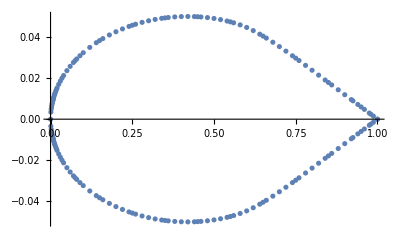

```mathematica
(* Reading airfoil *)
Filename="rae104.dat";
SetDirectory[NotebookDirectory[]];
xydata=ReadList[Filename, {Number, Number}];
xydata=Reverse[xydata];
ListPlot[xydata]
```

```mathematica
(* Parametric setting of the airfoil *)
chordParam = Table[0.,{Length[xydata]}];
For[i=1,i<=Length[xydata]-1,i++,
newChordLen=Sqrt[(xydata[[i+1]]-xydata[[i]]).(xydata[[i+1]]-xydata[[i]])];
chordParam[[i+1]]=chordParam[[i]]+newChordLen;
]

(* x(u) function *)
xuVertFunc=Partition[Riffle[chordParam,xydata[[All,1]]],2];
xu=Interpolation[xuVertFunc,Method->"Spline"];
(* y(u) function *)
yuVertFunc=Partition[Riffle[chordParam,xydata[[All,2]]],2];
yu=Interpolation[yuVertFunc,Method->"Spline"];
(* Check *)
xu[0]==xu[chordParam[[-1]]]
yu[0]==yu[chordParam[[-1]]]
```

True

True

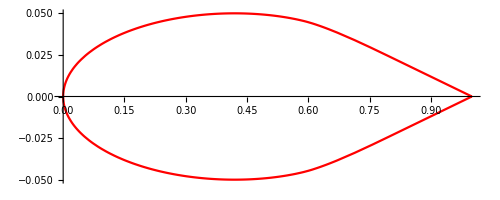

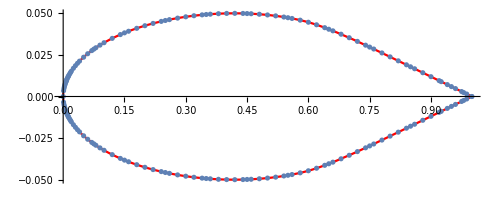

```mathematica
(* Airfoil visualisation *)
gr=ParametricPlot[{xu[u],yu[u]},{u,0,chordParam[[-1]]},PlotStyle->Red]
gr2=ListPlot[xydata];
Show[gr,gr2]
```

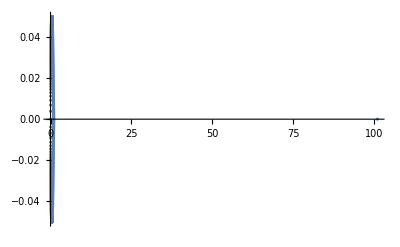

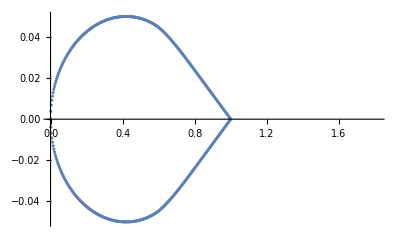

```mathematica
(* Setting airfoil with a large number of points, using interpolation *)
xy=Table[s=chordParam[[-1]]*(i-1)/(NN);
{xu[s],yu[s]},
{i,1,NN+1}];
AppendTo[xy,{xy[[NN+1,1]]+100,xy[[NN+1,2]]}];
ListPlot[xy,PlotRange->All]
ListPlot[xy]
```

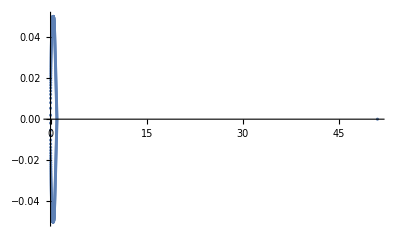

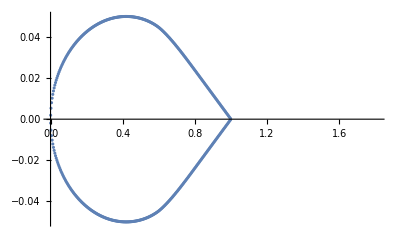

```mathematica
(* Collocations points *)
q=Table[(xy[[i]]+xy[[i+1]])/2,{i,1,NN+1}];
ListPlot[q,PlotRange->All]
ListPlot[q]
```

```mathematica
(* Direction of boundary element, tangentially to points q *)
ee=Table[(xy[[i+1]]-xy[[i]])/Sqrt[(xy[[i+1]]-xy[[i]]).(xy[[i+1]]-xy[[i]])],{i,1,NN+1}];
```

```mathematica
(* Calculating Subscript[D, ij]*)
Dij=Table[If[i==j,-1/2,0.],
{i,1,NN+1},{j,1,NN+1}];

Do[
Do[If[i!=j,
lengthElem=Sqrt[(xy[[j+1]]-xy[[j]]).(xy[[j+1]]-xy[[j]])];
x1=-lengthElem/2;
x2=lengthElem/2;
aVec=q[[i]]-q[[j]];
a1Prime=ee[[j,1]]*aVec[[1]]+ee[[j,2]]*aVec[[2]];
a2Prime=-ee[[j,2]]*aVec[[1]]+ee[[j,1]]*aVec[[2]];
Dij[[i,j]]=Douplet[a1Prime,a2Prime,x1,x2][[1]];
],
{j,1,NN+1}],
{i,1,NN}];
(* To effective use memory,E=D+I,D=D+I *)
Dij=Dij+IdentityMatrix[NN+1];
(* Set Zoukovsky-Chaplygin condition *)
Dij[[NN+1,1]]=1;
Dij[[NN+1,NN]]=-1;
Dij[[NN+1,NN+1]]=1;
```

```mathematica
(* Assembling right hand side of Morino equation *)
Rhs=Table[-uinf.q[[i]],{i,1,NN+1}];
(* Set Zoukovsky-Chaplygin condition *)
Rhs[[NN+1]]=0;
```

```mathematica
(* Obtain SLAE solution *)
nSolutionMu=LinearSolve[Dij,Rhs];
```

```mathematica
(* ϕ=-μ *)
nSolutionPhi=-nSolutionMu;

(* =-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=- *)
(* New chord parametrization *)
chordParamQ=Table[0.,{NN}];
(*chordParamQ[[1]]=Sqrt[(q[[1,1]]-q[[2,1]])^2+(q[[1,2]]-q[[2,2]])^2];*)
For[i=1,i<NN,i++,
newChordLen=Sqrt[(q[[i+1]]-q[[i]]).(q[[i+1]]-q[[i]])];
chordParamQ[[i+1]]=chordParamQ[[i]]+newChordLen;
]
(* =-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=- *)
(* Obtain interpolation solution *)
aSolutionPhi=Interpolation[Table[{chordParamQ[[i]],nSolutionPhi[[i]]},{i,1,NN}],Method->"Spline"];
```

```mathematica
(* Getting velocity magnitudes *)
V=Table[aSolutionPhi'[chordParamQ[[i]]],{i,1,NN}];
meshV=Partition[Riffle[chordParamQ,V],2];
```

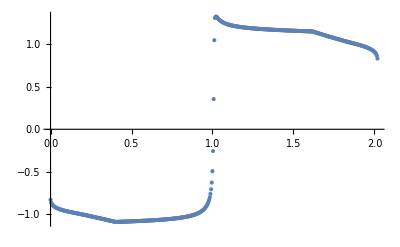

```mathematica
ListPlot[meshV]
```

```mathematica
(* Obtain Integral characteristics *)
XcompForce=-Sum[V[[j]]^2*(xy[[j+1,2]]-xy[[j,2]]),{j,1,NN}];
YcompForce=Sum[V[[j]]^2*(xy[[j+1,1]]-xy[[j,1]]),{j,1,NN}];
ResistForce =+ XcompForce*Cos[α]+YcompForce*Sin[α];
LiftForce =YcompForce*Cos[α]-XcompForce*Sin[α];
Print["Numeric: D = ", ResistForce, ", L = ", LiftForce]
Print["Analytic: D = ", 0, ", L = ",-2*nSolutionMu[[NN+1]]]
```

Numeric: D = -0.000604167, L = 0.235419

Analytic: D = 0, L = 0.23522